## 하나의 모듈로.

### 모델

```mathematica
(*metric model 입력*)
(*RNdS*)Δ1=r^2(1-(2 M)/r+Q^2/r^2-Λ/3 r^2);
```

```mathematica
1/2 D[Δ1/r^2,r]//FullSimplify
```

-Q^2/r^3+M/r^2-(r Λ)/3

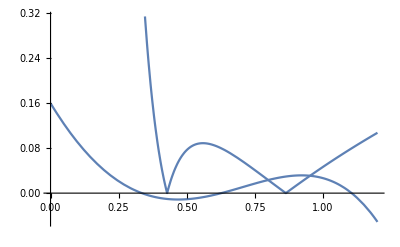

```mathematica
Plot[{Δ1,1/2 Abs[-Q^2/r^3+M/r^2-(r Λ)/3]}/.Λ->1/.M->0.4/.Q->0.4,{r,0,1.2}]
```

### code : RNdS1[M1_,Q1_,q1_,Ep_]

```mathematica
Clear[RNdS1];
RNdS1[M1_,Q1_,q1_,Ep_]:=Module[{(*M1,Q1,q1,Ep,*)Λ1,ri,ro,rc,rcircular,κm,κp,λcir,λovΩ,Ωcir},
(*Black hole 정보*)
(*M1=0.3;*)
(*Q1=M1;*)
Λ1=1;(*Λ=1일 때는 M=Q<0.45정도양지 솔루션들이 있음.*)
(*Particle 정보*)
(*Ep=1;*)
(*q1=1;*)

(*horizon 정하기*)
Module[{M,Q,Λ,Δ,sol,rh,sollength},
M=M1;
Q=Q1;
Λ=Λ1;
Δ[r_,M_,Q_,Λ_]=Δ1;
sol=NSolve[0==Δ[r,M,Q,Λ],r,Reals];
sollength=Length[sol];
If[sollength<3,Do[rh[i]=I,{i,1,sollength}],
Do[rh[i]=sol[[i,1,2]],{i,1,sollength}]];
ri=Catch[Do[If[rh[i]≥0,Throw[rh[i]]],{i,1,sollength}]];
ro=Catch[Do[If[rh[i]>ri,Throw[rh[i]]],{i,1,sollength}]];
rc=Catch[Do[If[rh[i]>ro,Throw[rh[i]]],{i,1,sollength}]];
(*rh[i]>ri;rh[i]>ro로 해놔서 extremal 경우엔 쓸수 없음.*)
];
(*radius of circular null geodesic*)
Module[{(*M,Q,Λ,*)Veff,En1,LL1,sol,rcir1,sollength,Δ},
Δ[r_,M_,Q_,Λ_]=Δ1;
(*potential model 입력 (circular null geodesic)*)
Veff[r_]=q^2((-En/q+Q/r)^2-(L/q)^2 1/r^2 Δ[r,M,Q,Λ]/r^2)/.L->√LL;
(*En1=Solve[Veff[r]==0,En][[2,1,2]];*)
LL1=Solve[0==D[Veff[r],r],LL][[1,1,2]];
sol=Solve[0==Veff[r]/.LL->LL1/.En->Ep/.q->q1/.M->M1/.Q->Q1/.Λ->Λ1,r];
sollength=Length[sol];
Do[rcir1[i]=sol[[i,1,2]],{i,1,sollength}];
(*Table[rcir1[i],{i,1,sollength}]*)
rcircular=Catch[Do[If[ro<rcir1[i]<rc,Throw[rcir1[i]]],{i,1,sollength}]];
];
(*Lyapunov exponent, nomalized Lyapunov 구하기.*)
Module[{Δ,rcir,M,Q,Λ},
M=M1;
Q=Q1;
Λ=Λ1;
Δ[r_,M_,Q_,Λ_]=Δ1;
rcir=rcircular;
λovΩ=(√((D[Δ[r,M,Q,Λ],r])^2/(4Δ[r,M,Q,Λ])+D[Δ[r,M,Q,Λ],r]/r-2 Δ[r,M,Q,Λ]/r^2-D[D[Δ[r,M,Q,Λ],r],r]/2)/.r->rcir);
Ωcir=(√Δ[rcir,M,Q,Λ])/rcir;
κm=Abs[1/2 D[Δ[r,M,Q,Λ],r]/.r->ri];
κp=Abs[1/2 D[Δ[r,M,Q,Λ],r]/.r->ro];
λcir=(1/2 √(1/r^6(-8 Δ[r,M,Q,Λ]^2+r^2 (D[Δ[r,M,Q,Λ],r])^2-2 r Δ[r,M,Q,Λ] (-2 D[Δ[r,M,Q,Λ],r]+r D[D[Δ[r,M,Q,Λ],r],r]))))/.r->rcir;
];
(*Print[{ri,ro,rc,rcircular,λovΩ,κm,λcir,λcir/κm}];*)
{Q1/M1,1/λcir,1/2 λcir/κm,1/(2π λovΩ),q1/Ep,(2π)/Ωcir,κp}
]
```

### lists1 M=0.4, 0.36(rc~ro)<Q<0.41(ri~ro)

```mathematica
Clear["Agraphλ*"]
```

```mathematica
Agraphλ02=Table[{RNdS1[0.4,Q,0.2,1][[1]],RNdS1[0.4,Q,0.2,1][[2]]},{Q,0.35,0.42,0.001}];
```

GreaterEqual::nord: Invalid comparison with ⅈ attempted.

Greater::nord: Invalid comparison with ⅈ attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

GreaterEqual::nord: Invalid comparison with ⅈ attempted.

General::stop: Further output of GreaterEqual::nord will be suppressed during this calculation.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

```mathematica
Agraphλ04=Table[{RNdS1[0.4,Q,0.4,1][[1]],RNdS1[0.4,Q,0.4,1][[2]]},{Q,0.35,0.42,0.001}];
Agraphλ06=Table[{RNdS1[0.4,Q,0.6,1][[1]],RNdS1[0.4,Q,0.6,1][[2]]},{Q,0.35,0.42,0.001}];
```

GreaterEqual::nord: Invalid comparison with ⅈ attempted.

Greater::nord: Invalid comparison with ⅈ attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

GreaterEqual::nord: Invalid comparison with ⅈ attempted.

General::stop: Further output of GreaterEqual::nord will be suppressed during this calculation.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

GreaterEqual::nord: Invalid comparison with ⅈ attempted.

Greater::nord: Invalid comparison with ⅈ attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

GreaterEqual::nord: Invalid comparison with ⅈ attempted.

General::stop: Further output of GreaterEqual::nord will be suppressed during this calculation.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

Less::nord: Invalid comparison with 0.574482-0.0390071 ⅈ attempted.

General::stop: Further output of Less::nord will be suppressed during this calculation.

```mathematica
Agraphλ08=Table[{RNdS1[0.4,Q,0.8,1][[1]],RNdS1[0.4,Q,0.8,1][[2]]},{Q,0.35,0.408,0.001}];
Agraphλ080=Table[{RNdS1[0.4,Q,0.8,1][[1]],RNdS1[0.4,Q,0.8,1][[2]]},{Q,0.408,0.413,0.0005}];
```

GreaterEqual::nord: Invalid comparison with ⅈ attempted.

Greater::nord: Invalid comparison with ⅈ attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Less::nord: Invalid comparison with 0.19182-0.0686968 ⅈ attempted.

General::stop: Further output of Less::nord will be suppressed during this calculation.

GreaterEqual::nord: Invalid comparison with ⅈ attempted.

General::stop: Further output of GreaterEqual::nord will be suppressed during this calculation.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

```mathematica
Agraphλ1=Table[{RNdS1[0.4,Q,1,1][[1]],RNdS1[0.4,Q,1,1][[2]]},{Q,0.35,0.408,0.001}];
Agraphλ10=Table[{RNdS1[0.4,Q,1,1][[1]],RNdS1[0.4,Q,1,1][[2]]},{Q,0.408,0.413,0.0002}]
```

GreaterEqual::nord: Invalid comparison with ⅈ attempted.

Greater::nord: Invalid comparison with ⅈ attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Less::nord: Invalid comparison with 0.210072-0.0992886 ⅈ attempted.

General::stop: Further output of Less::nord will be suppressed during this calculation.

GreaterEqual::nord: Invalid comparison with ⅈ attempted.

General::stop: Further output of GreaterEqual::nord will be suppressed during this calculation.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Less::nord: Invalid comparison with 0.347831-0.041549 ⅈ attempted.

General::stop: Further output of Less::nord will be suppressed during this calculation.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

{{1.02,5.98931},{1.0205,6.00443},{1.021,6.02085},{1.0215,6.03866},{1.022,6.05795},{1.0225,6.07884},{1.023,6.10145},{1.0235,6.12592},{1.024,6.1524},{1.0245,6.18108},{1.025,6.21214},{1.0255,6.24581},{1.026,6.28236},{1.0265,6.32207},{1.027,6.36528},{1.0275,6.41239},{1.028,6.46386},{1.0285,6.52023},{1.029,6.58215},{1.0295,6.6504},{1.03,6.7259},{1.0305,6.80981},{1.031,6.90356},{1.0315,7.00892},{1.032,7.12821},{1.0325,7.26442}}

```mathematica
Agraphκp1=Table[{RNdS1[0.4,Q,1,1][[1]],1/(RNdS1[0.4,Q,1,1][[7]])},{Q,0.35,0.42,0.001}]
```

GreaterEqual::nord: Invalid comparison with ⅈ attempted.

Greater::nord: Invalid comparison with ⅈ attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Less::nord: Invalid comparison with 0.210072-0.0992886 ⅈ attempted.

General::stop: Further output of Less::nord will be suppressed during this calculation.

GreaterEqual::nord: Invalid comparison with ⅈ attempted.

General::stop: Further output of GreaterEqual::nord will be suppressed during this calculation.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

{{0.875,2/Abs[(-0.245/Null^3+0.8/Null^2-(2 Null)/3) Null^2+2 Null (1+0.1225/Null^2-0.8/Null-Null^2/3)]},{0.8775,2/Abs[(-0.246402/Null^3+0.8/Null^2-(2 Null)/3) Null^2+2 Null (1+0.123201/Null^2-0.8/Null-Null^2/3)]},{0.88,2/Abs[(-0.247808/Null^3+0.8/Null^2-(2 Null)/3) Null^2+2 Null (1+0.123904/Null^2-0.8/Null-Null^2/3)]},{0.8825,2/Abs[(-0.249218/Null^3+0.8/Null^2-(2 Null)/3) Null^2+2 Null (1+0.124609/Null^2-0.8/Null-Null^2/3)]},{0.885,2/Abs[(-0.250632/Null^3+0.8/Null^2-(2 Null)/3) Null^2+2 Null (1+0.125316/Null^2-0.8/Null-Null^2/3)]},{0.8875,2/Abs[(-0.25205/Null^3+0.8/Null^2-(2 Null)/3) Null^2+2 Null (1+0.126025/Null^2-0.8/Null-Null^2/3)]},{0.89,2/Abs[(-0.253472/Null^3+0.8/Null^2-(2 Null)/3) Null^2+2 Null (1+0.126736/Null^2-0.8/Null-Null^2/3)]},{0.8925,2/Abs[(-0.254898/Null^3+0.8/Null^2-(2 Null)/3) Null^2+2 Null (1+0.127449/Null^2-0.8/Null-Null^2/3)]},{0.895,2/Abs[(-0.256328/Null^3+0.8/Null^2-(2 Null)/3) Null^2+2 Null (1+0.128164/Null^2-0.8/Null-Null^2/3)]},{0.8975,57.1397},{0.9,37.3948},{0.9025,30.2867},{0.905,26.3646},{0.9075,23.8074},{0.91,21.9819},{0.9125,20.6022},{0.915,19.5182},{0.9175,18.6424},{0.92,17.92},{0.9225,17.3146},{0.925,16.8011},{0.9275,16.3616},{0.93,15.9829},{0.9325,15.655},{0.935,15.3703},{0.9375,15.1229},{0.94,14.9081},{0.9425,14.722},{0.945,14.5619},{0.9475,14.4252},{0.95,14.31},{0.9525,14.2148},{0.955,14.1384},{0.9575,14.0798},{0.96,14.0382},{0.9625,14.0133},{0.965,14.0047},{0.9675,14.0124},{0.97,14.0363},{0.9725,14.0769},{0.975,14.1345},{0.9775,14.2099},{0.98,14.304},{0.9825,14.418},{0.985,14.5534},{0.9875,14.7122},{0.99,14.8966},{0.9925,15.1096},{0.995,15.3549},{0.9975,15.6369},{1.,15.9614},{1.0025,16.3357},{1.005,16.7695},{1.0075,17.2752},{1.01,17.8699},{1.0125,18.5771},{1.015,19.4304},{1.0175,20.48},{1.02,21.8047},{1.0225,23.5363},{1.025,25.9177},{1.0275,29.46},{1.03,35.5027},{1.0325,49.5086},{1.035,2/Abs[(-0.342792/Null^3+0.8/Null^2-(2 Null)/3) Null^2+2 Null (1+0.171396/Null^2-0.8/Null-Null^2/3)]},{1.0375,2/Abs[(-0.34445/Null^3+0.8/Null^2-(2 Null)/3) Null^2+2 Null (1+0.172225/Null^2-0.8/Null-Null^2/3)]},{1.04,2/Abs[(-0.346112/Null^3+0.8/Null^2-(2 Null)/3) Null^2+2 Null (1+0.173056/Null^2-0.8/Null-Null^2/3)]},{1.0425,2/Abs[(-0.347778/Null^3+0.8/Null^2-(2 Null)/3) Null^2+2 Null (1+0.173889/Null^2-0.8/Null-Null^2/3)]},{1.045,2/Abs[(-0.349448/Null^3+0.8/Null^2-(2 Null)/3) Null^2+2 Null (1+0.174724/Null^2-0.8/Null-Null^2/3)]},{1.0475,2/Abs[(-0.351122/Null^3+0.8/Null^2-(2 Null)/3) Null^2+2 Null (1+0.175561/Null^2-0.8/Null-Null^2/3)]},{1.05,2/Abs[(-0.3528/Null^3+0.8/Null^2-(2 Null)/3) Null^2+2 Null (1+0.1764/Null^2-0.8/Null-Null^2/3)]}}

```mathematica
Clear["AgraphΩ*"]
```

```mathematica
AgraphΩ1=Table[{RNdS1[0.4,Q,1,1][[1]],RNdS1[0.4,Q,1,1][[6]]},{Q,0.35,0.408,0.001}];
AgraphΩ10=Table[{RNdS1[0.4,Q,1,1][[1]],RNdS1[0.4,Q,1,1][[6]]},{Q,0.408,0.413,0.0002}];
```

GreaterEqual::nord: Invalid comparison with ⅈ attempted.

Greater::nord: Invalid comparison with ⅈ attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Less::nord: Invalid comparison with 0.210072-0.0992886 ⅈ attempted.

General::stop: Further output of Less::nord will be suppressed during this calculation.

GreaterEqual::nord: Invalid comparison with ⅈ attempted.

General::stop: Further output of GreaterEqual::nord will be suppressed during this calculation.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Less::nord: Invalid comparison with 0.347831-0.041549 ⅈ attempted.

General::stop: Further output of Less::nord will be suppressed during this calculation.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

```mathematica
AgraphΩ02=Table[{RNdS1[0.4,Q,0.2,1][[1]],RNdS1[0.4,Q,0.2,1][[6]]},{Q,0.35,0.42,0.001}];
AgraphΩ04=Table[{RNdS1[0.4,Q,0.4,1][[1]],RNdS1[0.4,Q,0.4,1][[6]]},{Q,0.35,0.42,0.001}];
AgraphΩ06=Table[{RNdS1[0.4,Q,0.6,1][[1]],RNdS1[0.4,Q,0.6,1][[6]]},{Q,0.35,0.42,0.001}];
AgraphΩ08=Table[{RNdS1[0.4,Q,0.8,1][[1]],RNdS1[0.4,Q,0.8,1][[6]]},{Q,0.35,0.42,0.001}];
```

GreaterEqual::nord: Invalid comparison with ⅈ attempted.

Greater::nord: Invalid comparison with ⅈ attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

GreaterEqual::nord: Invalid comparison with ⅈ attempted.

General::stop: Further output of GreaterEqual::nord will be suppressed during this calculation.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

GreaterEqual::nord: Invalid comparison with ⅈ attempted.

Greater::nord: Invalid comparison with ⅈ attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

GreaterEqual::nord: Invalid comparison with ⅈ attempted.

General::stop: Further output of GreaterEqual::nord will be suppressed during this calculation.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

GreaterEqual::nord: Invalid comparison with ⅈ attempted.

Greater::nord: Invalid comparison with ⅈ attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

GreaterEqual::nord: Invalid comparison with ⅈ attempted.

General::stop: Further output of GreaterEqual::nord will be suppressed during this calculation.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

Less::nord: Invalid comparison with 0.574482-0.0390071 ⅈ attempted.

General::stop: Further output of Less::nord will be suppressed during this calculation.

GreaterEqual::nord: Invalid comparison with ⅈ attempted.

Greater::nord: Invalid comparison with ⅈ attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Less::nord: Invalid comparison with 0.19182-0.0686968 ⅈ attempted.

General::stop: Further output of Less::nord will be suppressed during this calculation.

GreaterEqual::nord: Invalid comparison with ⅈ attempted.

General::stop: Further output of GreaterEqual::nord will be suppressed during this calculation.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

```mathematica
Clear["AgraphλovΩ*"]
```

```mathematica
AgraphλovΩ1=Table[{RNdS1[0.4,Q,1,1][[1]],RNdS1[0.4,Q,1,1][[4]]},{Q,0.35,0.408,0.001}];
AgraphλovΩ10=Table[{RNdS1[0.4,Q,1,1][[1]],RNdS1[0.4,Q,1,1][[4]]},{Q,0.408,0.413,0.0002}];
```

GreaterEqual::nord: Invalid comparison with ⅈ attempted.

Greater::nord: Invalid comparison with ⅈ attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Less::nord: Invalid comparison with 0.210072-0.0992886 ⅈ attempted.

General::stop: Further output of Less::nord will be suppressed during this calculation.

GreaterEqual::nord: Invalid comparison with ⅈ attempted.

General::stop: Further output of GreaterEqual::nord will be suppressed during this calculation.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Less::nord: Invalid comparison with 0.347831-0.041549 ⅈ attempted.

General::stop: Further output of Less::nord will be suppressed during this calculation.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

```mathematica
AgraphλovΩ02=Table[{RNdS1[0.4,Q,0.2,1][[1]],RNdS1[0.4,Q,0.2,1][[4]]},{Q,0.35,0.42,0.001}];
AgraphλovΩ04=Table[{RNdS1[0.4,Q,0.4,1][[1]],RNdS1[0.4,Q,0.4,1][[4]]},{Q,0.35,0.42,0.001}];
AgraphλovΩ06=Table[{RNdS1[0.4,Q,0.6,1][[1]],RNdS1[0.4,Q,0.6,1][[4]]},{Q,0.35,0.42,0.001}];
```

GreaterEqual::nord: Invalid comparison with ⅈ attempted.

Greater::nord: Invalid comparison with ⅈ attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

GreaterEqual::nord: Invalid comparison with ⅈ attempted.

General::stop: Further output of GreaterEqual::nord will be suppressed during this calculation.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

GreaterEqual::nord: Invalid comparison with ⅈ attempted.

Greater::nord: Invalid comparison with ⅈ attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

GreaterEqual::nord: Invalid comparison with ⅈ attempted.

General::stop: Further output of GreaterEqual::nord will be suppressed during this calculation.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

GreaterEqual::nord: Invalid comparison with ⅈ attempted.

Greater::nord: Invalid comparison with ⅈ attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

GreaterEqual::nord: Invalid comparison with ⅈ attempted.

General::stop: Further output of GreaterEqual::nord will be suppressed during this calculation.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

Less::nord: Invalid comparison with 0.574482-0.0390071 ⅈ attempted.

General::stop: Further output of Less::nord will be suppressed during this calculation.

```mathematica
AgraphλovΩ08=Table[{RNdS1[0.4,Q,0.8,1][[1]],RNdS1[0.4,Q,0.8,1][[4]]},{Q,0.35,0.408,0.001}];
AgraphλovΩ080=Table[{RNdS1[0.4,Q,0.8,1][[1]],RNdS1[0.4,Q,0.8,1][[4]]},{Q,0.408,0.413,0.0005}];
```

GreaterEqual::nord: Invalid comparison with ⅈ attempted.

Greater::nord: Invalid comparison with ⅈ attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Less::nord: Invalid comparison with 0.19182-0.0686968 ⅈ attempted.

General::stop: Further output of Less::nord will be suppressed during this calculation.

GreaterEqual::nord: Invalid comparison with ⅈ attempted.

General::stop: Further output of GreaterEqual::nord will be suppressed during this calculation.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

### graphs

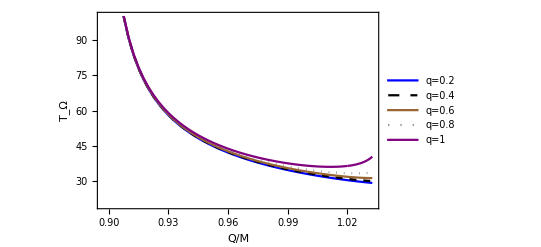

```mathematica
(*time_Omega1*)ListPlot[{AgraphΩ02,AgraphΩ04,AgraphΩ06,AgraphΩ08,AgraphΩ1,AgraphΩ10},Joined->True,PlotRange->{{0.897,1.033},{20,100(*270*)}},AxesOrigin->{0,0},FrameLabel->{Style["Q/M",13],Style["T_Ω",13]},Frame->True,Axes->False,PlotLegends->Placed[{"q=0.2","q=0.4","q=0.6","q=0.8","q=1"},{Right,Top}],PlotStyle->{Blue,{Black,Dashed},Brown,{Gray,Dotted},Purple,Purple}]
```

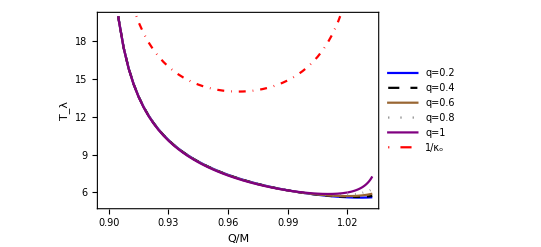

```mathematica
(*time_Lyapu1*)ListPlot[{Agraphλ02,Agraphλ04,Agraphλ06,Agraphλ08,Agraphλ1,Agraphκp1,Agraphλ080,Agraphλ10},Joined->True,PlotRange->{{0.897,1.033},{5,20(*45*)}},AxesOrigin->{0,0},FrameLabel->{Style["Q/M",13],Style["T_λ",13]},Frame->True,Axes->False,PlotLegends->Placed[{"q=0.2","q=0.4","q=0.6","q=0.8","q=1","1/κ_o"},{Right,Top}],PlotStyle->{Blue,{Black,Dashed},Brown,{Gray,Dotted},Purple,{Red,DotDashed},{Gray,Dotted},Purple}]
```

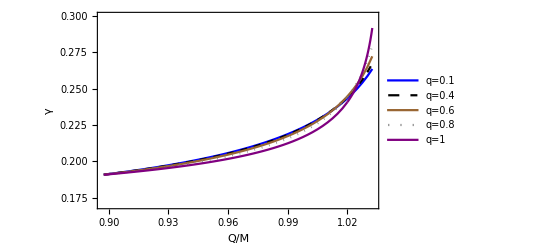

```mathematica
(*time_Omega_Lyapu1*)ListPlot[{AgraphλovΩ02,AgraphλovΩ04,AgraphλovΩ06,AgraphλovΩ08,AgraphλovΩ1,AgraphλovΩ080,AgraphλovΩ10},Joined->True,PlotRange->{{0.897,1.033},{0.17,0.3}},AxesOrigin->{0,0},Frame->True,Axes->False,PlotLegends->Placed[{"q=0.1","q=0.4","q=0.6","q=0.8","q=1"},{Left,Top}],FrameLabel->{Style["Q/M",13],Style["γ",13]},PlotStyle->{Blue,{Black,Dashed},Brown,{Gray,Dotted},Purple,{Gray,Dotted},Purple}]
```

```mathematica
0.4*0.97
```

0.388

```mathematica
{0.36/0.4,0.372/0.4,0.388/0.4,0.4/0.4,0.412/0.4}//N
```

{0.9,0.93,0.97,1.,1.03}

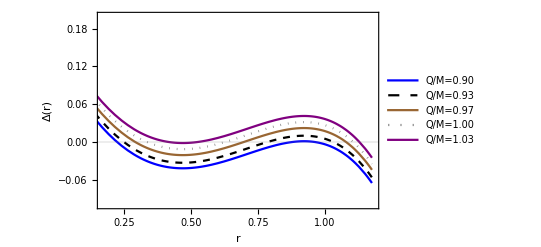

```mathematica
Plot[{r^2(1-(2 M)/r+Q^2/r^2-Λ/3 r^2)/.M->0.4/.Λ->1/.Q->0.36,r^2(1-(2 M)/r+Q^2/r^2-Λ/3 r^2)/.M->0.4/.Λ->1/.Q->0.372,r^2(1-(2 M)/r+Q^2/r^2-Λ/3 r^2)/.M->0.4/.Λ->1/.Q->0.388,r^2(1-(2 M)/r+Q^2/r^2-Λ/3 r^2)/.M->0.4/.Λ->1/.Q->0.4,r^2(1-(2 M)/r+Q^2/r^2-Λ/3 r^2)/.M->0.4/.Λ->1/.Q->0.412},{r,0,1.175},PlotRange->{{0.17,1.18},{-0.1,0.2}},AxesOrigin->{0.1,0},Frame->True,Axes->False,FrameLabel->{Style["r",15],Style["Δ(r)",13]},GridLines->{{},{{0,{Black,Thin}}}},PlotLegends->Placed[{"Q/M=0.90","Q/M=0.93","Q/M=0.97","Q/M=1.00","Q/M=1.03"},{Left,Top}],PlotStyle->{Blue,{Black,Dashed},Brown,{Gray,Dotted},Purple}]
```

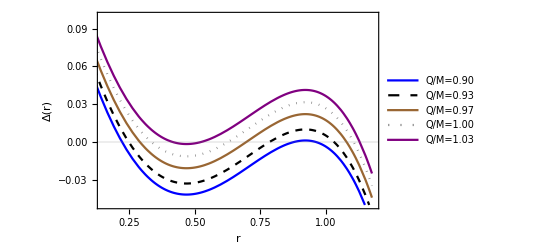

```mathematica
Plot[{r^2(1-(2 M)/r+Q^2/r^2-Λ/3 r^2)/.M->0.4/.Λ->1/.Q->0.36,r^2(1-(2 M)/r+Q^2/r^2-Λ/3 r^2)/.M->0.4/.Λ->1/.Q->0.372,r^2(1-(2 M)/r+Q^2/r^2-Λ/3 r^2)/.M->0.4/.Λ->1/.Q->0.388,r^2(1-(2 M)/r+Q^2/r^2-Λ/3 r^2)/.M->0.4/.Λ->1/.Q->0.4,r^2(1-(2 M)/r+Q^2/r^2-Λ/3 r^2)/.M->0.4/.Λ->1/.Q->0.412},{r,0,1.175},PlotRange->{{0.15,1.18},{-0.05,0.1}},AxesOrigin->{0.1,0},Frame->True,Axes->False,FrameLabel->{Style["r",15],Style["Δ(r)",13]},GridLines->{{},{{0,{Black,Thin}}}},PlotLegends->Placed[{"Q/M=0.90","Q/M=0.93","Q/M=0.97","Q/M=1.00","Q/M=1.03"},{Left,Top}(*{Center,Top}*)],PlotStyle->{Blue,{Black,Dashed},Brown,{Gray,Dotted},Purple}]
```

```mathematica
Plot[{r^2(1-(2 M)/r+Q^2/r^2-Λ/3 r^2)/.M->0.4/.Λ->1/.Q->0.36,r^2(1-(2 M)/r+Q^2/r^2-Λ/3 r^2)/.M->0.4/.Λ->1/.Q->0.372,r^2(1-(2 M)/r+Q^2/r^2-Λ/3 r^2)/.M->0.4/.Λ->1/.Q->0.388,r^2(1-(2 M)/r+Q^2/r^2-Λ/3 r^2)/.M->0.4/.Λ->1/.Q->0.4,r^2(1-(2 M)/r+Q^2/r^2-Λ/3 r^2)/.M->0.4/.Λ->1/.Q->0.412},{r,0,1.175},PlotRange->{{0.15,1.18},{-0.05,0.1}},AxesOrigin->{0.1,0},Frame->True,Axes->False,FrameLabel->{Style["r",15],Style["Δ(r)",13]},GridLines->{{},{{0,{Black,Thin}}}},PlotLegends->Placed[{"Q/M=0.90","Q/M=0.93","Q/M=0.97","Q/M=1.00","Q/M=1.03"},{0.26,Top}(*{Center,Top}*)],PlotStyle->{Blue,{Black,Dashed},Brown,{Gray,Dotted},Purple}]
```

-Graphics-

### Q 고정, M 변화에 따른 그래프, M이 0으로 가게되면 r_o=r_c limit 이 안생김.

#### Try and error

```mathematica
{0.1*0.94,0.1*1.02}
```

{0.094,0.102}

```mathematica
{0.388/0.377,0.388/0.385,0.388/0.395,0.388/0.4,0.388/0.4115}
```

{1.02918,1.00779,0.982278,0.97,0.942892}

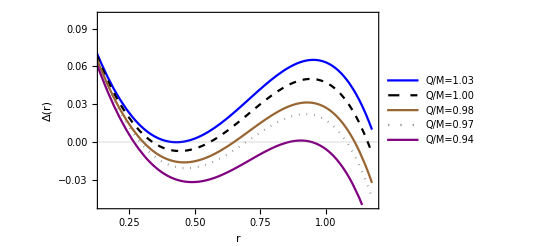

```mathematica
Plot[{r^2(1-(2 M)/r+Q^2/r^2-Λ/3 r^2)/.M->0.377/.Λ->1/.Q->0.388,r^2(1-(2 M)/r+Q^2/r^2-Λ/3 r^2)/.M->0.385/.Λ->1/.Q->0.388,r^2(1-(2 M)/r+Q^2/r^2-Λ/3 r^2)/.M->0.395/.Λ->1/.Q->0.388,r^2(1-(2 M)/r+Q^2/r^2-Λ/3 r^2)/.M->0.4/.Λ->1/.Q->0.388,r^2(1-(2 M)/r+Q^2/r^2-Λ/3 r^2)/.M->0.4115/.Λ->1/.Q->0.388},{r,0,1.175},PlotRange->{{0.15,1.18},{-0.05,0.1}},AxesOrigin->{0.1,0},Frame->True,Axes->False,FrameLabel->{Style["r",15],Style["Δ(r)",13]},GridLines->{{},{{0,{Black,Thin}}}},PlotLegends->Placed[{"Q/M=1.03","Q/M=1.00","Q/M=0.98","Q/M=0.97","Q/M=0.94"},{Left,Top}(*{Center,Top}*)],PlotStyle->{Blue,{Black,Dashed},Brown,{Gray,Dotted},Purple}]
```

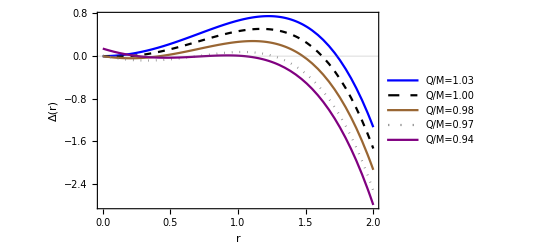

```mathematica
Plot[{r^2(1-(2 M)/r+Q^2/r^2-Λ/3 r^2)/.M->0/.Λ->1/.Q->0,r^2(1-(2 M)/r+Q^2/r^2-Λ/3 r^2)/.M->0.1/.Λ->1/.Q->0.0001,r^2(1-(2 M)/r+Q^2/r^2-Λ/3 r^2)/.M->0.2/.Λ->1/.Q->0.0001,r^2(1-(2 M)/r+Q^2/r^2-Λ/3 r^2)/.M->0.3/.Λ->1/.Q->0.1,r^2(1-(2 M)/r+Q^2/r^2-Λ/3 r^2)/.M->0.4/.Λ->1/.Q->0.376},{r,0,2},PlotRange->All(*{{0.15,1.18},{-0.05,0.1}}*),AxesOrigin->{0.1,0},Frame->True,Axes->False,FrameLabel->{Style["r",15],Style["Δ(r)",13]},GridLines->{{},{{0,{Black,Thin}}}},PlotLegends->Placed[{"Q/M=1.03","Q/M=1.00","Q/M=0.98","Q/M=0.97","Q/M=0.94"},{Left,Bottom}(*{Center,Top}*)],PlotStyle->{Blue,{Black,Dashed},Brown,{Gray,Dotted},Purple}]
```

#### 고정 Q, 변수 M에 따른 r_o, r_c

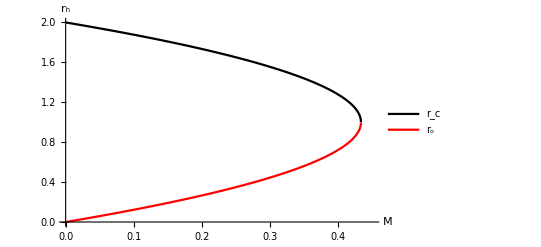

```mathematica
(*EX) MTZ black hole*)Plot[{1+√(1-4M √(1/3)),1-√(1-4M √(1/3))},{M,0,0.45},PlotStyle->{Black, Red},PlotLegends->{"r_c","r_o"},AxesLabel
->{"M","r_h"}]
```

```mathematica
(*horizon 정하기*)
horizon[M1_,Q1_]:=Module[{M,Q,Λ,Δ,sol,rh,sollength,ro,rc},
M=M1;
Q=Q1;
Λ=1;
Δ[r_,M_,Q_,Λ_]=Δ1;
sol=NSolve[0==Δ[r,M,Q,Λ],r,Reals];
sollength=Length[sol];
If[sollength<3,Do[rh[i]=I,{i,1,sollength}],
Do[rh[i]=sol[[i,1,2]],{i,1,sollength}]];
ri=Catch[Do[If[rh[i]≥0,Throw[rh[i]]],{i,1,sollength}]];
ro=Catch[Do[If[rh[i]>ri,Throw[rh[i]]],{i,1,sollength}]];
rc=Catch[Do[If[rh[i]>ro,Throw[rh[i]]],{i,1,sollength}]];
{M1,ro,rc}
]
```

```mathematica
0.377,0.4115
```

```mathematica
Manipulate[Plot[r^2(1-(2 M)/r+Q^2/r^2-Λ/3 r^2)/.Λ->1/.Q->0.1,{r,0,1.3},AxesOrigin->{0,0}],{M,0,0.339}]
```

```mathematica
0.2/0.3
```

0.666667

```mathematica
{0.388/0.411,0.2/0.351,0.1/0.337,0.01/0.33}
```

{0.944039,0.569801,0.296736,0.030303}

```mathematica
{horizon[0.411,0.388],horizon[0.351,0.2],horizon[0.337,0.1],horizon[0.33,0.01],horizon[0.33,0.001],horizon[0.33,0]}
```

{{0.411,0.84445,0.958866},{0.351,0.90405,1.05157},{0.337,0.942164,1.04675},{0.33,0.916515,1.08112},{0.33,0.917193,1.08058},{0.33,0.9172,1.08057}}

```mathematica
listro=Table[{horizon[M,0.388][[1]],horizon[M,0.388][[2]]},{M,0.36,0.43,0.0001}];
listrc=Table[{horizon[M,0.388][[1]],horizon[M,0.388][[3]]},{M,0.36,0.43,0.0001}];
```

GreaterEqual::nord: Invalid comparison with ⅈ attempted.

Greater::nord: Invalid comparison with ⅈ attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

GreaterEqual::nord: Invalid comparison with ⅈ attempted.

General::stop: Further output of GreaterEqual::nord will be suppressed during this calculation.

GreaterEqual::nord: Invalid comparison with ⅈ attempted.

Greater::nord: Invalid comparison with ⅈ attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

GreaterEqual::nord: Invalid comparison with ⅈ attempted.

General::stop: Further output of GreaterEqual::nord will be suppressed during this calculation.

```mathematica
listro1=Table[{horizon[M,0.2][[1]],horizon[M,0.2][[2]]},{M,0.188,0.36,0.0001}];
listrc1=Table[{horizon[M,0.2][[1]],horizon[M,0.2][[3]]},{M,0.188,0.36,0.0001}];
```

GreaterEqual::nord: Invalid comparison with ⅈ attempted.

Greater::nord: Invalid comparison with ⅈ attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

GreaterEqual::nord: Invalid comparison with ⅈ attempted.

General::stop: Further output of GreaterEqual::nord will be suppressed during this calculation.

GreaterEqual::nord: Invalid comparison with ⅈ attempted.

Greater::nord: Invalid comparison with ⅈ attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

GreaterEqual::nord: Invalid comparison with ⅈ attempted.

General::stop: Further output of GreaterEqual::nord will be suppressed during this calculation.

```mathematica
listro2=Table[{horizon[M,0.1][[1]],horizon[M,0.1][[2]]},{M,0,0.339,0.0001}];
listrc2=Table[{horizon[M,0.1][[1]],horizon[M,0.1][[3]]},{M,0,0.339,0.0001}];
```

GreaterEqual::nord: Invalid comparison with ⅈ attempted.

Greater::nord: Invalid comparison with ⅈ attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

GreaterEqual::nord: Invalid comparison with ⅈ attempted.

General::stop: Further output of GreaterEqual::nord will be suppressed during this calculation.

GreaterEqual::nord: Invalid comparison with ⅈ attempted.

Greater::nord: Invalid comparison with ⅈ attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

GreaterEqual::nord: Invalid comparison with ⅈ attempted.

General::stop: Further output of GreaterEqual::nord will be suppressed during this calculation.

```mathematica
listro3=Table[{horizon[M,0][[1]],horizon[M,0][[2]]},{M,0.0001,0.34,0.0001}];
listrc3=Table[{horizon[M,0][[1]],horizon[M,0][[3]]},{M,0,0.34,0.0001}];
```

GreaterEqual::nord: Invalid comparison with ⅈ attempted.

Greater::nord: Invalid comparison with ⅈ attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

GreaterEqual::nord: Invalid comparison with ⅈ attempted.

General::stop: Further output of GreaterEqual::nord will be suppressed during this calculation.

GreaterEqual::nord: Invalid comparison with ⅈ attempted.

Greater::nord: Invalid comparison with ⅈ attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

GreaterEqual::nord: Invalid comparison with ⅈ attempted.

General::stop: Further output of GreaterEqual::nord will be suppressed during this calculation.

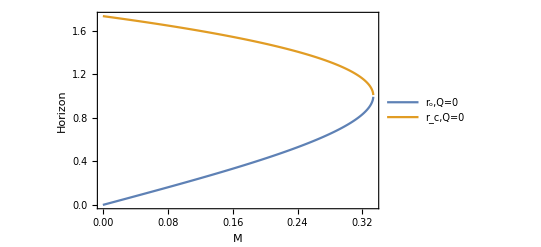

```mathematica
ListPlot[{(*listro,listrc,listro1,listrc1,*)listro3,listrc3},Joined->True,Frame->True,Axes->False,FrameLabel->{Style["M",15],Style["Horizon",15]},(*GridLines->{{},{{0,{Black,Thin}}}},*)PlotLegends->Placed[{(*"r_o,Q=0.39","r_c,Q=0.39","r_o,Q=0.2","r_c,Q=0.2",*)"r_o,Q=0","r_c,Q=0"},{Right,Bottom}(*{Center,Top}*)](*,PlotStyle->{Brown,{Gray,Dashed}}*)]
```

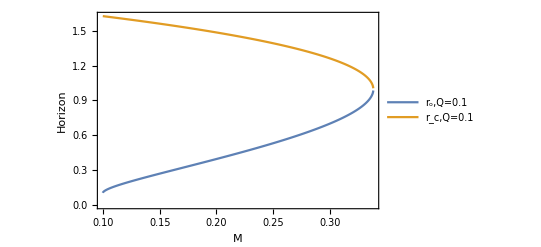

```mathematica
ListPlot[{(*listro,listrc,listro1,listrc1,*)listro2,listrc2},Joined->True,Frame->True,Axes->False,FrameLabel->{Style["M",15],Style["Horizon",15]},(*GridLines->{{},{{0,{Black,Thin}}}},*)PlotLegends->Placed[{(*"r_o,Q=0.39","r_c,Q=0.39","r_o,Q=0.2","r_c,Q=0.2",*)"r_o,Q=0.1","r_c,Q=0.1"},{Right,Bottom}(*{Center,Top}*)](*,PlotStyle->{Brown,{Gray,Dashed}}*)]
```

## 각 모듈별로 쪼개 놓은것.

```mathematica
Clear[M2,Q2,Λ2,rcircular2]

(*Black hole 정보*)
M2=0.4;Q2=0.36;
Λ2=1;(*Λ=1일 때는 M=Q<0.44정도에서 호라이즌 솔루션들이 있음.*)
(*Particle 정보*)
Ep2=1;
q2=2;
(*metric model 입력*)
Δ1=r^2(1-(2 M)/r+Q^2/r^2-Λ/3 r^2);
```

```mathematica
Manipulate[Plot[r^2(1-(2 M)/r+Q^2/r^2-Λ2/3 r^2)/.M->M2,{r,0,1.5},AxesOrigin->{0,0},AxesLabel->{"r","Δ[r]"}],{Q,0,0.31}];
```

```mathematica
Clear[ri,ro,rc];
(*horizon 정하기*)
Module[{M,Q,Λ,Δ,sol,rh,sollength},
M=M2;
Q=Q2;
Λ=Λ2;
Δ[r_,M_,Q_,Λ_]=Δ1;
sol=NSolve[0==Δ[r,M,Q,Λ],r,Reals];
sollength=Length[sol];
If[sollength<3,Do[rh[i]=I,{i,1,sollength}],
Do[rh[i]=sol[[i,1,2]],{i,1,sollength}]];
ri=Catch[Do[If[rh[i]≥0,Throw[rh[i]]],{i,1,sollength}]];
ro=Catch[Do[If[rh[i]>ri,Throw[rh[i]]],{i,1,sollength}]];
rc=Catch[Do[If[rh[i]>ro,Throw[rh[i]]],{i,1,sollength}]];
Print[{ri,ro,rc}];
]
```

{0.223284,0.878063,0.961389}

```mathematica
(*ϵc=*)(2ro (ro^2-ri^2))/(ri^2(3ro+ri))
```

8.8895

```mathematica
(*Mass=(-Λ/3)(rc1 ro1 ri1-(ro1 ri1+rc1 (ro1+ri1)) rn)/2/.rn->rc1+ro1+ri1/.Λ->Λ2;
charge=(√rc1 √ro1 √ri1 √rn √Λ)/(√3)/.rn->rc1+ro1+ri1/.Λ->Λ2;*)
```

```mathematica
(*radius of circular null geodesic*)
Module[{(*M,Q,Λ,*)Veff,En1,LL1,sol,rcir1,sollength,Δ},
Δ[r_,M_,Q_,Λ_]=Δ1;
(*potential model 입력 (circular null geodesic)*)
Veff[r_]=q^2((-En/q+Q/r)^2-(L/q)^2 1/r^2 Δ[r,M,Q,Λ]/r^2)/.L->√LL;
(*En1=Solve[Veff[r]==0,En][[2,1,2]];*)
LL1=Solve[0==D[Veff[r],r],LL][[1,1,2]];
sol=Solve[0==Veff[r]/.LL->LL1/.En->Ep2/.q->q2/.M->M2/.Q->Q2/.Λ->Λ2,r];
sollength=Length[sol];
Do[rcir1[i]=sol[[i,1,2]],{i,1,sollength}];
(*Table[rcir1[i],{i,1,sollength}]*)
rcircular2=Catch[Do[If[ro<rcir1[i]<rc,Throw[rcir1[i]]],{i,1,sollength}]];
Print[rcircular2];
]
```

0.834038

```mathematica
(*Lyapunov exponent, nomalized Lyapunov 구하기.*)
Module[{λovΩ,Δ,rcir,M,Q,Λ,κm,λcir},
M=M2;
Q=Q2;
Λ=Λ2;
Δ[r_,M_,Q_,Λ_]=Δ1;
rcir=rcircular2;
λovΩ=(√((D[Δ[r,M,Q,Λ],r])^2/(4Δ[r,M,Q,Λ])+D[Δ[r,M,Q,Λ],r]/r-2 Δ[r,M,Q,Λ]/r^2-D[D[Δ[r,M,Q,Λ],r],r]/2)/.r->rcir);
κm=Abs[1/2 D[Δ[r,M,Q,Λ],r]/.r->ri];
λcir=(1/2 √(1/r^6(-8 Δ[r,M,Q,Λ]^2+r^2 (D[Δ[r,M,Q,Λ],r])^2-2 r Δ[r,M,Q,Λ] (-2 D[Δ[r,M,Q,Λ],r]+r D[D[Δ[r,M,Q,Λ],r],r]))))/.r->rcir;
{λovΩ,κm,λcir,λcir/κm}
]
```

{1.02579,0.16554,0.0931899,0.562946}